```mathematica
R=1 ;
L=2;
Subscript[L, 2]=3;
ω=1;
α=-π/2;
b = 10;
T=2π/ω;
time=2π;
dt=0.01;
maxX=R+L+Subscript[L, 2];
minX=L+Subscript[L, 2]-R;
```

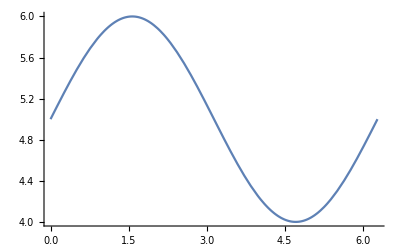

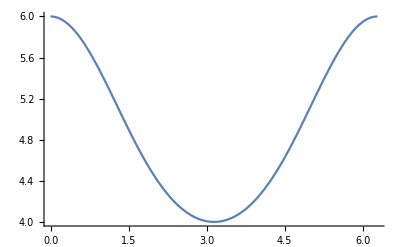

```mathematica
(*x(t)*)
Subscript[x, τ][t_]:=R Cos[ω t+α]+Subscript[L, 2]+ L;

(*x(φ)*)
Subscript[x, φ][f_] := R Cos[f]+√(Subscript[L, 2]^2-(R Sin[f])^2)+L;

Plot[Subscript[x, τ][t],{t,0,time}]
Plot[Subscript[x, φ][f],{f,0,2π}]
```

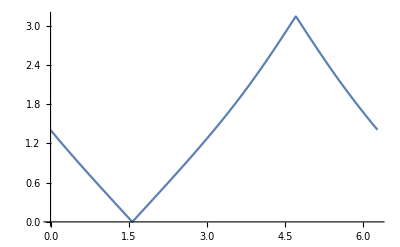

```mathematica
phi=Table[FindRoot[Subscript[x, τ][t]==Subscript[x, φ][f],{f,1}][[1,2]],{t,0,time,dt}];
times=Range[0,time,dt];
ListLinePlot[Table[{times[[i]],phi[[i]]},{i,1,Length[times]}]]
```

{{-6.28,0.166667+0.986013 ⅈ},{-6.27,0.176096+0.984373 ⅈ},{-6.26,0.185495+0.982645 ⅈ},1253,{6.27,0.154188+0.988041 ⅈ},{6.28,0.163657+0.986517 ⅈ}}
 |  |  |  |

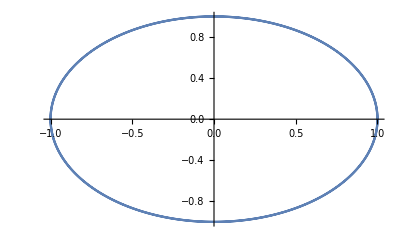

```mathematica
expphi=Exp[I*phi];
expphi=Join[Table[{-times[[Length[times]+1-i]],expphi[[i]]},{i,1,Length[times]}],Table[{times[[i]],expphi[[i]]},{i,1,Length[times]}]]
ListLinePlot[Table[{Re[expphi[[i]][[2]]], Im[expphi[[i]][[2]]]}, {i,1,2Length[times]}]]
```

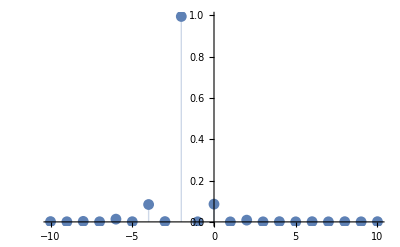

<|-10→0.000177978+0.00149063 ⅈ,-9→0.000107592+0.000626463 ⅈ,-8→-0.00227659+0.00105186 ⅈ,-7→0.000150311+0.000656391 ⅈ,-6→0.000245457-0.0132707 ⅈ,-5→0.000256523+0.000878194 ⅈ,-4→0.0840753+0.00133913 ⅈ,-3→-0.0000859397+0.00151868 ⅈ,-2→-0.0013996+0.993708 ⅈ,-1→0.0000302186-0.0005006 ⅈ,0→0.0859656+0.0010675 ⅈ,1→0.0000517009+0.000163021 ⅈ,2→0.000188661+0.008429 ⅈ,3→0.0000618954+0.000310827 ⅈ,4→-0.000456795+0.00107393 ⅈ,5→0.0000644804+0.000362646 ⅈ,6→0.000181069+0.00101437 ⅈ,7→0.0000686269+0.000392674 ⅈ,8→0.000183984+0.00106751 ⅈ,9→0.000071112+0.000412234 ⅈ,10→0.000176951+0.00107018 ⅈ|>

```mathematica
numberOfCoeffs= 10;
fourierCoeffs = Association[Table[i->1/(2T)Total[Map[#[[2]] Exp[-I π i  (#[[1]])/T]dt &, expphi]],{i, -numberOfCoeffs,numberOfCoeffs}]];
ListPlot[fourierCoeffs //Abs, PlotRange->All, Filling->Axis]
fourierCoeffs
```